```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1035.53 ⅈ,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{{1},12,{1}}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

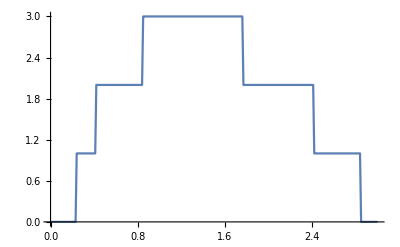

```mathematica
ListLinePlot[pris]
```

```mathematica
μ1=RandomInteger[{1,14}]; μ2=RandomInteger[{1,14}]; μ3=RandomInteger[{1,14}]; μ4=RandomInteger[{1,14}];μ5=RandomInteger[{1,14}]; μ6=RandomInteger[{1,14}]; μ7=RandomInteger[{1,14}];μ8=RandomInteger[{1,14}]; μ9=RandomInteger[{1,14}]; μ10=RandomInteger[{1,14}]; μ11=RandomInteger[{1,14}];μ12=RandomInteger[{1,14}]; μ13=RandomInteger[{1,14}];   μ14=RandomInteger[{1,14}]
```

6

```mathematica
RandomSample[{imp14,imp,imp,imp,imp5,imp14,imp,imp,imp11,imp,imp6,imp,imp13,imp3,imp9,imp,imp11,imp13,imp,imp12,imp8,imp,imp,imp,imp4,imp,imp12,imp8,imp7,imp5,imp,imp,imp,imp9,imp,imp1,imp1,imp,imp14,imp,imp10,imp12,imp6,imp10,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp3,imp,imp,imp9,imp,imp6,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp10,imp4,imp,imp4,imp,imp,imp,imp,imp,imp3,imp1,imp2,imp8,imp5,imp,imp,imp7,imp,imp,imp2,imp,imp,imp,imp}]
```

{imp12,imp,imp,imp,imp5,imp14,imp,imp2,imp3,imp,imp,imp,imp9,imp7,imp10,imp,imp,imp9,imp,imp4,imp8,imp,imp12,imp,imp7,imp1,imp,imp10,imp,imp3,imp,imp,imp,imp4,imp,imp,imp,imp13,imp,imp,imp,imp6,imp,imp6,imp11,imp,imp,imp,imp,imp,imp,imp5,imp,imp8,imp4,imp8,imp1,imp,imp7,imp9,imp,imp,imp,imp1,imp,imp,imp,imp11,imp,imp,imp,imp,imp14,imp,imp13,imp,imp,imp11,imp14,imp2,imp,imp,imp,imp,imp10,imp,imp13,imp,imp,imp2,imp5,imp,imp,imp,imp,imp,imp12,imp6,imp3,imp}

```mathematica
Tally[%66]
```

{{imp12,3},{imp,58},{imp5,3},{imp14,3},{imp2,3},{imp3,3},{imp9,3},{imp7,3},{imp10,3},{imp4,3},{imp8,3},{imp1,3},{imp13,3},{imp6,3},{imp11,3}}

```mathematica
Dimensions[%20]
```

{100}

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp]
```

```mathematica
Table[RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],1]],Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},7],0]],Table[imp,36]]],50]
```

```mathematica
Dimensions[%307]
```

{100}

```mathematica
impu[ω_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ=RandomInteger[{1,14}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
impu2[ω_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ=RandomInteger[{1,14}]},μ1=RandomChoice[Delete[Range[1,14,1],μ],1][[1]];ReplacePart[κ,{{μ,μ},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
data[n_,ω_,ϵ1_,a_,c_,num_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={{imp12,imp,imp,imp,imp5,imp14,imp,imp2,imp3,imp,imp,imp1,imp9,imp7,imp10,imp,imp,imp9,imp,imp4,imp8,imp,imp12,imp,imp7,imp1,imp,imp10,imp,imp3,imp,imp,imp,imp4,imp,imp,imp,imp13,imp,imp,imp,imp6,imp,imp6,imp11,imp,imp,imp,imp1,imp,imp,imp5,imp,imp8,imp4,imp8,imp1,imp,imp7,imp9,imp,imp,imp,imp1,imp,imp,imp,imp11,imp,imp,imp,imp,imp14,imp,imp13,imp,imp,imp11,imp14,imp2,imp,imp,imp,imp,imp10,imp,imp13,imp,imp,imp2,imp5,imp,imp,imp,imp,imp,imp12,imp6,imp3,imp}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,a,c}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
trans[n_,a_,b_,num_]:= ParallelTable[{ω,data[n,ω,0.5,a,b,num]},{ω,Range[0,3,0.01]}]
```

```mathematica
input={trans[1,1,100,0]}
```

{{{0.,2.8×10^-7},{0.01,1.65494×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.155614},{0.25,0.146975},{0.26,0.125367},{0.27,0.65135},{0.28,0.391477},{0.29,0.878021},{0.3,0.561816},{0.31,0.899615},{0.32,0.354057},{0.33,0.230605},{0.34,0.270825},{0.35,0.747067},{0.36,0.487805},{0.37,0.560641},{0.38,0.730322},{0.39,0.715463},{0.4,0.790031},{0.41,0.744739},{0.42,0.392996},{0.43,0.809447},{0.44,1.50999},{0.45,0.964177},{0.46,0.831576},{0.47,0.678807},{0.48,0.703829},{0.49,0.86678},{0.5,0.629855},{0.51,1.10646},{0.52,0.903601},{0.53,0.389109},{0.54,0.991032},{0.55,0.910123},{0.56,1.1097},{0.57,0.55012},{0.58,1.14194},{0.59,0.742984},{0.6,1.02291},{0.61,1.18039},{0.62,1.38732},{0.63,0.807739},{0.64,0.91782},{0.65,1.12858},{0.66,1.04938},{0.67,1.34977},{0.68,0.66535},{0.69,0.978469},{0.7,0.647708},{0.71,1.36853},{0.72,1.16188},{0.73,1.02523},{0.74,1.1387},{0.75,1.16376},{0.76,1.71944},{0.77,1.16831},{0.78,0.938738},{0.79,1.47116},{0.8,0.899996},{0.81,1.33729},{0.82,1.20966},{0.83,0.734707},{0.84,0.808609},{0.85,0.238511},{0.86,0.351115},{0.87,0.474491},{0.88,0.904544},{0.89,0.643705},{0.9,0.153354},{0.91,0.425868},{0.92,0.0672614},{0.93,0.552447},{0.94,0.747529},{0.95,1.86399},{0.96,1.26089},{0.97,0.881109},{0.98,1.68984},{0.99,1.63262},{1.,1.5554},{1.01,1.96577},{1.02,1.64888},{1.03,1.54921},{1.04,1.00365},{1.05,0.0025157},{1.06,0.435996},{1.07,0.430564},{1.08,0.167111},{1.09,0.541761},{1.1,0.10214},{1.11,0.252375},{1.12,0.645771},{1.13,0.479771},{1.14,1.00288},{1.15,1.02075},{1.16,1.02426},{1.17,0.634475},{1.18,1.05327},{1.19,1.05742},{1.2,0.934421},{1.21,0.930624},{1.22,1.15449},{1.23,1.23164},{1.24,1.07399},{1.25,0.526344},{1.26,1.0374},{1.27,0.659864},{1.28,1.25386},{1.29,1.85916},{1.3,1.26623},{1.31,1.40477},{1.32,1.17361},{1.33,1.36218},{1.34,1.84013},{1.35,1.11708},{1.36,0.73967},{1.37,0.968688},{1.38,0.800544},{1.39,1.68379},{1.4,1.21319},{1.41,1.11002},{1.42,0.976356},{1.43,0.895983},{1.44,1.19129},{1.45,1.83116},{1.46,1.59577},{1.47,0.998688},{1.48,0.947284},{1.49,0.504028},{1.5,0.529308},{1.51,0.89921},{1.52,1.40386},{1.53,1.68858},{1.54,0.121069},{1.55,0.529052},{1.56,0.973462},{1.57,1.52457},{1.58,0.110344},{1.59,0.0760085},{1.6,1.23777},{1.61,0.895967},{1.62,1.01884},{1.63,0.330421},{1.64,0.245211},{1.65,0.750714},{1.66,0.99112},{1.67,0.293657},{1.68,0.932253},{1.69,0.641175},{1.7,0.0028078},{1.71,0.907865},{1.72,0.340529},{1.73,0.288557},{1.74,0.596781},{1.75,2.15606},{1.76,2.31578},{1.77,2.00012},{1.78,0.488765},{1.79,0.242553},{1.8,0.0813543},{1.81,0.421184},{1.82,0.119071},{1.83,0.825808},{1.84,0.839081},{1.85,0.682453},{1.86,0.434665},{1.87,0.729519},{1.88,0.49979},{1.89,0.755597},{1.9,0.642946},{1.91,0.486754},{1.92,0.643762},{1.93,0.679873},{1.94,0.516467},{1.95,0.809205},{1.96,0.465162},{1.97,1.02169},{1.98,1.13161},{1.99,0.761788},{2.,1.07457},{2.01,0.950135},{2.02,0.957227},{2.03,0.30639},{2.04,0.855973},{2.05,1.36137},{2.06,0.6619},{2.07,1.47466},{2.08,0.40971},{2.09,0.561999},{2.1,0.813104},{2.11,0.71824},{2.12,0.810603},{2.13,0.410279},{2.14,0.392045},{2.15,1.23995},{2.16,0.26549},{2.17,0.749439},{2.18,0.872972},{2.19,0.951172},{2.2,1.08267},{2.21,0.345371},{2.22,0.778373},{2.23,0.185532},{2.24,0.719962},{2.25,0.209871},{2.26,0.91063},{2.27,0.350521},{2.28,0.837413},{2.29,0.0723507},{2.3,0.321735},{2.31,0.542219},{2.32,0.933533},{2.33,0.635186},{2.34,0.250305},{2.35,0.717983},{2.36,0.27308},{2.37,0.960411},{2.38,0.122231},{2.39,0.385458},{2.4,0.0817021},{2.41,1.99986},{2.42,0.539545},{2.43,0.300631},{2.44,0.225177},{2.45,0.798331},{2.46,0.842949},{2.47,0.108895},{2.48,0.100217},{2.49,0.216862},{2.5,0.311893},{2.51,0.846805},{2.52,0.496619},{2.53,0.818747},{2.54,0.497144},{2.55,0.187517},{2.56,0.190743},{2.57,0.100069},{2.58,0.386912},{2.59,0.228386},{2.6,0.126509},{2.61,0.553331},{2.62,0.231791},{2.63,0.399322},{2.64,0.142579},{2.65,0.865905},{2.66,0.657246},{2.67,0.0991767},{2.68,0.162924},{2.69,0.796297},{2.7,0.203634},{2.71,0.560529},{2.72,0.128292},{2.73,0.0784657},{2.74,0.0806824},{2.75,0.062642},{2.76,0.114013},{2.77,0.935935},{2.78,0.308356},{2.79,0.119112},{2.8,0.179706},{2.81,0.0506296},{2.82,0.224012},{2.83,0.424686},{2.84,0.0184938},{2.85,0.000342218},{2.86,0.0000162888},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}}

```mathematica
r50[n_,x_]:=υ50[n,1.6,0,x]
```

```mathematica
r100[n_]:=υ100[n,1.6,0]
```

```mathematica
r20[n_]:=Table[υ20[n,1.6,0,x],{x,Range[1,90,20]}]
```

```mathematica
r20new[n_]:=Table[υ20[n,1.6,0,x],{x,Range[10,70,20]}]
```

```mathematica
r10[n_]:=Join[Table[υ10[n,1.6,0,a],{a,Range[1,90,10]}],{υ10[n,1.6,0,90]}]
```

```mathematica
transmission100=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[ξ]<>".dat"],{ξ,Range[1,148,2]}]
```

{{{0.,2.8×10^-7},{0.01,2.78688×10^-7},{0.02,2.81426×10^-7},{0.03,2.86149×10^-7},{0.04,2.91921×10^-7},{0.05,2.99702×10^-7},{0.06,3.104×10^-7},{0.07,3.236×10^-7},{0.08,3.39098×10^-7},{0.09,3.60208×10^-7},{0.1,3.83774×10^-7},{0.11,4.16428×10^-7},{0.12,4.55823×10^-7},275,{2.88,2.35076×10^-6},{2.89,1.36206×10^-6},{2.9,8.85392×10^-7},{2.91,6.21742×10^-7},{2.92,4.60063×10^-7},{2.93,3.54141×10^-7},{2.94,2.80823×10^-7},{2.95,2.27859×10^-7},{2.96,1.88758×10^-7},{2.97,1.58734×10^-7},{2.98,1.35435×10^-7},{2.99,1.16828×10^-7},{3.,1.02002×10^-7}},72,{1}}
 |  |  |  |

```mathematica
transmission50=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/50unitcells/resolve/test"<>ToString[ξ]<>".dat"],{ξ,Range[1,49,1]}]
```

{{{0.,2.8×10^-7},{0.01,2.78387×10^-7},{0.02,2.79591×10^-7},{0.03,2.85054×10^-7},{0.04,2.90787×10^-7},{0.05,2.9891×10^-7},{0.06,3.09097×10^-7},{0.07,3.21204×10^-7},{0.08,3.373×10^-7},{0.09,3.56989×10^-7},{0.1,3.83461×10^-7},{0.11,4.13729×10^-7},{0.12,4.51436×10^-7},275,{2.88,2.34469×10^-6},{2.89,1.3577×10^-6},{2.9,8.8166×10^-7},{2.91,6.19652×10^-7},{2.92,4.5788×10^-7},{2.93,3.52972×10^-7},{2.94,2.79993×10^-7},{2.95,2.2733×10^-7},{2.96,1.88536×10^-7},{2.97,1.58682×10^-7},{2.98,1.35059×10^-7},{2.99,1.16697×10^-7},{3.,1.01915×10^-7}},47,{1}}
 |  |  |  |

```mathematica
Dimensions[%48]
```

{49,301,2}

```mathematica
transmission20=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/resolve/test"<>ToString[ξ]<>".dat"],{ξ,Range[1,20,1]}]
```

{{{0.,2.8×10^-7},{0.01,2.73752×10^-7},{0.02,2.7484×10^-7},{0.03,2.80462×10^-7},{0.04,2.85798×10^-7},{0.05,2.93081×10^-7},{0.06,3.03595×10^-7},{0.07,3.16031×10^-7},{0.08,3.30954×10^-7},{0.09,3.4915×10^-7},{0.1,3.73937×10^-7},{0.11,4.04373×10^-7},{0.12,4.4308×10^-7},275,{2.88,2.33765×10^-6},{2.89,1.35253×10^-6},{2.9,8.72262×10^-7},{2.91,6.14279×10^-7},{2.92,4.52921×10^-7},{2.93,3.51046×10^-7},{2.94,2.79282×10^-7},{2.95,2.26668×10^-7},{2.96,1.88385×10^-7},{2.97,1.58159×10^-7},{2.98,1.34437×10^-7},{2.99,1.15914×10^-7},{3.,1.01334×10^-7}},18,{1}}
 |  |  |  |

```mathematica
transmission10=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/resolve/test"<>ToString[ξ]<>".dat"],{ξ,Range[1,10,1]}]
```

{{{0.,2.8×10^-7},{0.01,2.66273×10^-7},{0.02,2.68969×10^-7},{0.03,2.73358×10^-7},{0.04,2.76658×10^-7},{0.05,2.87086×10^-7},{0.06,2.96518×10^-7},{0.07,3.08402×10^-7},{0.08,3.2189×10^-7},{0.09,3.40853×10^-7},{0.1,3.6261×10^-7},{0.11,3.88808×10^-7},{0.12,4.26463×10^-7},275,{2.88,2.29778×10^-6},{2.89,1.33265×10^-6},{2.9,8.6186×10^-7},{2.91,6.06692×10^-7},{2.92,4.48771×10^-7},{2.93,3.48761×10^-7},{2.94,2.77989×10^-7},{2.95,2.25631×10^-7},{2.96,1.87027×10^-7},{2.97,1.57074×10^-7},{2.98,1.34095×10^-7},{2.99,1.15036×10^-7},{3.,1.00302×10^-7}},8,{1}}
 |  |  |  |

```mathematica
input={trans[1,1,10,0],trans[1,11,20,0],trans[1,21,30,0],trans[1,31,40,0],trans[1,41,50,0],trans[1,51,60,0],trans[1,61,70,0],trans[1,71,80,0],trans[1,81,90,0],trans[1,91,100,0]}
```

{{{0.,2.78283×10^-7},{0.01,1.84028×10^-7},{0.02,1.94605×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},275,{2.88,2.35363×10^-6},{2.89,1.30986×10^-6},{2.9,8.42709×10^-7},{2.91,5.95654×10^-7},{2.92,4.44698×10^-7},{2.93,3.44861×10^-7},{2.94,2.75196×10^-7},{2.95,2.2461×10^-7},{2.96,1.86715×10^-7},{2.97,1.576×10^-7},{2.98,1.34757×10^-7},{2.99,1.16512×10^-7},{3.,1.01714×10^-7}},8,{1}}
 |  |  |  |

```mathematica
Dimensions[input]
```

{9,50,301,2}

```mathematica
input=Table[trans[n,1,100,1],{n,10}]
```

{1}
 |  |  |  |

```mathematica
Dimensions[transmission20]
```

{20,301,2}

```mathematica
υnew[n_,num_,x_,y_]:=Module[{m5=input[[n]]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-transmission100[[ξ]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,74}];
{ρ1}]
```

```mathematica
υnew[1,0,2.95,0]
```

{{1.82425,1.42315,1.14599,0.93997,0.779978,0.652618,0.550782,0.466485,0.399386,0.342328,0.295776,0.255649,0.224191,0.197737,0.176432,0.159597,0.144528,0.133021,0.123915,0.117562,0.111973,0.109404,0.106292,0.105681,0.105346,0.106256,0.108113,0.110003,0.11302,0.115198,0.119649,0.123573,0.12673,0.131581,0.135499,0.140276,0.145195,0.149772,0.154085,0.158966,0.164275,0.168736,0.173106,0.17857,0.182704,0.188719,0.193637,0.197363,0.200313,0.205626,0.213488,0.217286,0.222694,0.22653,0.229457,0.233978,0.237675,0.240845,0.24547,0.248083,0.251924,0.254998,0.258396,0.261726,0.264256,0.266871,0.270225,0.273493,0.276767,0.279129,0.28064,0.284499,0.286837,0.28911}}

```mathematica
Transpose[Join[{Range[1,147,2]},{Flatten[υnew[1,0,2.95,0]]}]]
```

{{1,1.82425},{3,1.42315},{5,1.14599},{7,0.93997},{9,0.779978},{11,0.652618},{13,0.550782},{15,0.466485},{17,0.399386},{19,0.342328},{21,0.295776},{23,0.255649},{25,0.224191},{27,0.197737},{29,0.176432},{31,0.159597},{33,0.144528},{35,0.133021},{37,0.123915},{39,0.117562},{41,0.111973},{43,0.109404},{45,0.106292},{47,0.105681},{49,0.105346},{51,0.106256},{53,0.108113},{55,0.110003},{57,0.11302},{59,0.115198},{61,0.119649},{63,0.123573},{65,0.12673},{67,0.131581},{69,0.135499},{71,0.140276},{73,0.145195},{75,0.149772},{77,0.154085},{79,0.158966},{81,0.164275},{83,0.168736},{85,0.173106},{87,0.17857},{89,0.182704},{91,0.188719},{93,0.193637},{95,0.197363},{97,0.200313},{99,0.205626},{101,0.213488},{103,0.217286},{105,0.222694},{107,0.22653},{109,0.229457},{111,0.233978},{113,0.237675},{115,0.240845},{117,0.24547},{119,0.248083},{121,0.251924},{123,0.254998},{125,0.258396},{127,0.261726},{129,0.264256},{131,0.266871},{133,0.270225},{135,0.273493},{137,0.276767},{139,0.279129},{141,0.28064},{143,0.284499},{145,0.286837},{147,0.28911}}

```mathematica
Position[%89,Min[%89]]
```

{{25,2}}

```mathematica
%79[[25]]
```

{49,0.114087}

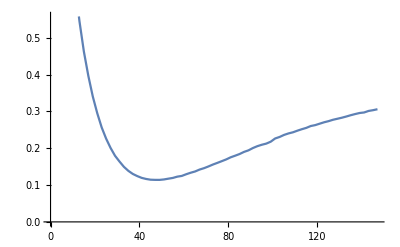

```mathematica
ListPlot[%79,Joined->True]
```

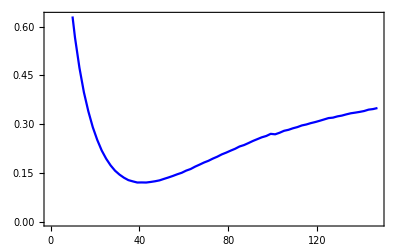

```mathematica
ListPlot[%36,Joined->True,Frame->True,PlotStyle->Blue]
```

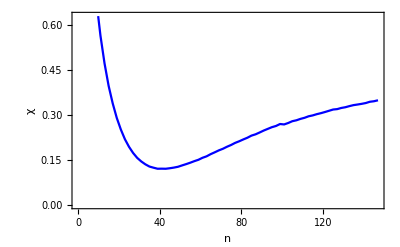

```mathematica
Show[%57,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
cba=Table[Transpose[Join[{Range[1,147,2]},{Flatten[υnew[n,0,2.95,0]]}]],{n,1}]
```

{{{1,1.69382},{3,1.29299},{5,1.02529},{7,0.830729},{9,0.682084},{11,0.565753},{13,0.473001},{15,0.398096},{17,0.339508},{19,0.290702},{21,0.251856},{23,0.219402},{25,0.194154},{27,0.173606},{29,0.157263},{31,0.145279},{33,0.135731},{35,0.12828},{37,0.124433},{39,0.120936},{41,0.121156},{43,0.120892},{45,0.122636},{47,0.124779},{49,0.127516},{51,0.132052},{53,0.136392},{55,0.141087},{57,0.146289},{59,0.150865},{61,0.15752},{63,0.162398},{65,0.169675},{67,0.17582},{69,0.182297},{71,0.187624},{73,0.194417},{75,0.200295},{77,0.207338},{79,0.212752},{81,0.218861},{83,0.224544},{85,0.231623},{87,0.235946},{89,0.24206},{91,0.248538},{93,0.254165},{95,0.259797},{97,0.263804},{99,0.270353},{101,0.268972},{103,0.273769},{105,0.279742},{107,0.28278},{109,0.287492},{111,0.291148},{113,0.296207},{115,0.299122},{117,0.303261},{119,0.306574},{121,0.310447},{123,0.314593},{125,0.318774},{127,0.320159},{129,0.32401},{131,0.326449},{133,0.330198},{135,0.333498},{137,0.335525},{139,0.33779},{141,0.340468},{143,0.344697},{145,0.346437},{147,0.34965}}}

```mathematica
abc=Table[cba[[x]][[Position[cba[[x]],Min[cba[[x]]]][[1,1]]]],{x,10}]//Sort
```

{{2,0.0125572},{2,0.0136214},{4,0.0276657},{4,0.0343161},{4,0.0359979},{4,0.0372549},{4,0.0391882},{5,0.0520621},{7,0.0407508},{7,0.0538266}}

```mathematica
Join[Table[a1,2],Table[a2,2],Table[b1,3],Table[b2,4],Table[c1,4],Table[c2,4],Table[d1,4],Table[d2,5],Table[e1,7],Table[e2,7]]
```

{a1,a1,a2,a2,b1,b1,b1,b2,b2,b2,b2,c1,c1,c1,c1,c2,c2,c2,c2,d1,d1,d1,d1,d2,d2,d2,d2,d2,e1,e1,e1,e1,e1,e1,e1,e2,e2,e2,e2,e2,e2,e2}

```mathematica
Tally[{a1,a1,a2,a2,b1,b1,b1,b2,b2,b2,b2,c1,c1,c1,c1,c2,c2,c2,c2,d1,d1,d1,d1,d2,d2,d2,d2,d2,e1,e1,e1,e1,e1,e1,e1,e2,e2,e2,e2,e2,e2,e2}]
```

{{a1,2},{a2,2},{b1,3},{b2,4},{c1,4},{c2,4},{d1,4},{d2,5},{e1,7},{e2,7}}

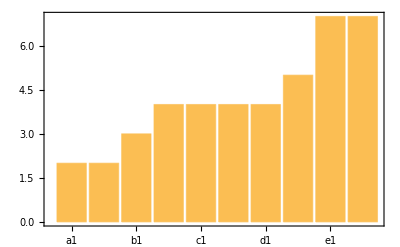

```mathematica
BarChart[Apply[Labeled,Reverse[{{a1,2},{a2,2},{b1,3},{b2,4},{c1,4},{c2,4},{d1,4},{d2,5},{e1,7},{e2,7}},2],{1}],Frame->True]
```

```mathematica
Dimensions[%77]
```

{10,2}

```mathematica
Join[Table[a b c/2,18],Table[c/2de,22]]
```

{(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(a b c)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2,(c de)/2}

```mathematica
Tally[%54]
```

{{(a b c)/2,18},{(c de)/2,22}}

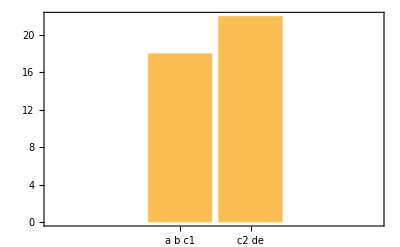

```mathematica
BarChart[Apply[Labeled,Reverse[{{a b (c1),18},{c2 de,22}},2],{1}],Frame->True]
```

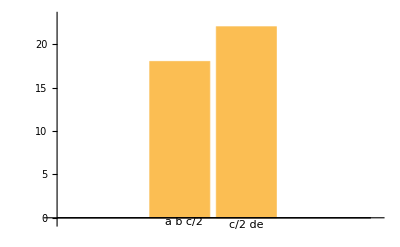

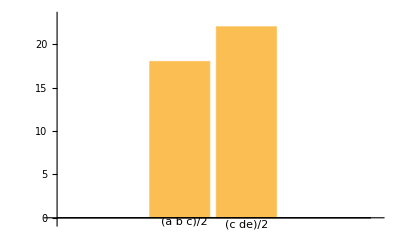

```mathematica
Join[Table[a,6],Table[b,7],Table[c,9],Table[d,10],Table[e,11]]
```

{a,a,a,a,a,a,b,b,b,b,b,b,b,c,c,c,c,c,c,c,c,c,d,d,d,d,d,d,d,d,d,d,e,e,e,e,e,e,e,e,e,e,e}

```mathematica
Tally[{a,a,a,a,a,a,b,b,b,b,b,b,b,c,c,c,c,c,c,c,c,c,d,d,d,d,d,d,d,d,d,d,e,e,e,e,e,e,e,e,e,e,e}]
```

{{a,6},{b,7},{c,9},{d,10},{e,11}}

```mathematica
BarChart[Apply[Labeled,Reverse[{{a,6},{b,7},{c,9},{d,10},{e,11}},2],{1}],Frame->True]
```

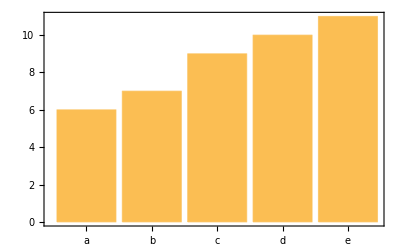

-Graphics-

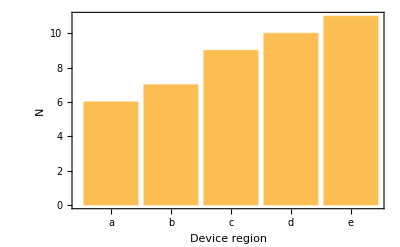

```mathematica
Show[%54,FrameLabel->{{HoldForm[N],None},{HoldForm[Device region],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
%84
```

-Graphics-

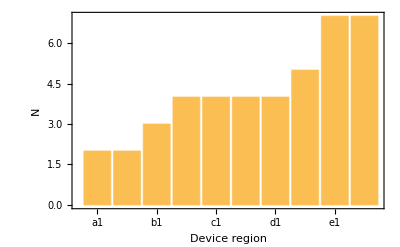

```mathematica
Show[%55,FrameLabel->{{HoldForm[N],None},{HoldForm[Device region],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
%65
```

-Graphics-

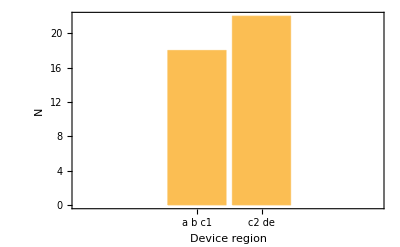

```mathematica
Show[%56,FrameLabel->{{HoldForm[N],None},{HoldForm[Device region],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```